```mathematica
2-2
```

0

# Site-specific Hexagonal Walks 4

Nicholas Wheeler
16 January 2012

### Introduction

In "Hexagonal Walks" (1 December 2011) I devised an elementary technique for constructing unbiased site-independent random walks on a hexagonal lattice

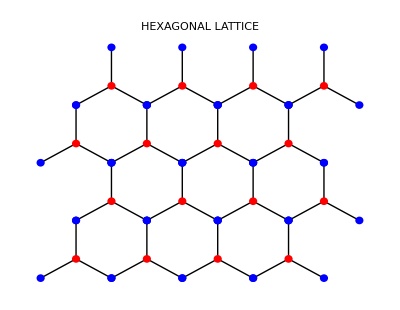

The problem is made challenging by the simple fact that the walker confronts distinct next-step options

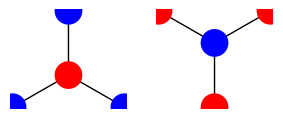

depending upon whether he stands momentarily on a ● node or a ● node (which he is obliged to do in strict alternation). The walks generated in the notebook just mentioned look typically like this

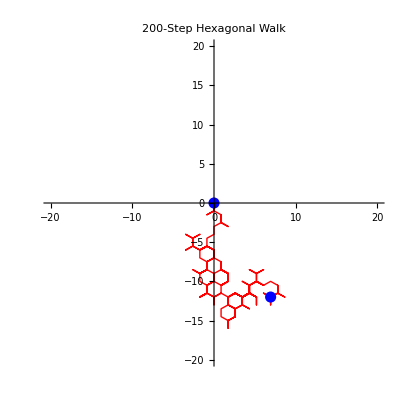

and were "unbiased and site-independent" in the sense that wherever the walker stands he is equally likely to step to any of the three adjacent nodes. 

In "Site-specific Hexagonal Walks 1" (29 December 2011) I relaxed the "unbiased" assumption

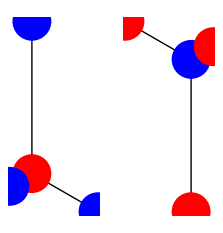

REMARK: Here I use arrow-length to signify not step-length but step-probability (or "weight").

while preserving site-independence…which proved to be easy, and produced walks that look typically like this

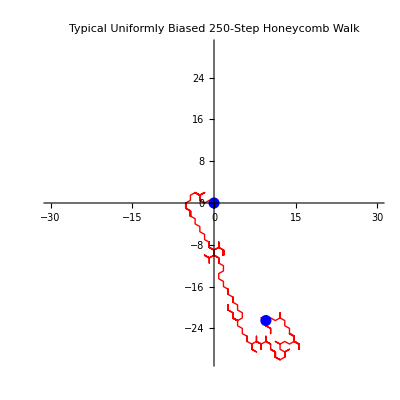

Here I made essential use of the weighted generalization

RandomChoice[{w_1,w_2,w_3→{X_1,X_2,X_3}}]

of the RandomChoice command, but proceeded otherwise by always the same 2-step process:

• Construct a random sequence of steps

S_1,S_2,S_3,S_4,S_5, ... ,S_200

• String them together, to create walks:

S_1
S_1+S_2
S_1+S_2+S_3
⋮

I devised several relatively brief composite commands that are capable of accomplishing such constructions.

But none of those constructions proved capable—the working title of the notebook just cited is "Generalizations of the Nest Command," which alludes to my unrealized objective—of accommodating site-specificity, nor any of the other recursive procedures I attempted. All failed to keep track of the "present location" that is needed by the walker to determine his local step weights, and all had difficulty with the alternating node color aspect of the problem. So—ignorant as I presently am of the Mathematica programming techniques that I am confident would reduce the problem to a triviality—I was forced to fall back upon the tedious "by hand" procedure described in the next section.

### "By hand" construction of hexagonal walks with site-specific weights

The step options are described

```mathematica
R1=N[{Cos[π/2],Sin[π/2]}];
R2=N[{Cos[π/2-4(2π)/12],Sin[π/2-4(2π)/12]}];
R3=N[{Cos[π/2-8(2π)/12],Sin[π/2-8(2π)/12]}];
B1=-R1;
B2=-R2;
B3=-R3;
```

which are displayed as red ℛ-vectors and blue ℬ-vectors in the following figure:

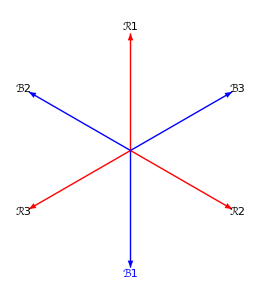

To construct a 100-step walk we have first to describe the site-specific weight functions, which will have the form

wr[x_,y_]:={r_1[x,y],r_2[x,y],r_3[x,y]}
wb[x_,y_]:={b_1[x,y],b_2[x,y],b_3[x,y]}

and then to execute (repeatedly,  to gain a sense of the situation) the series of 100 commands that are presented below.

REMARK: I have been unable to devise a master command that generates those sequential commands automatically, was forced to write them out by hand.

#### Unbiased site-nonspecific walks

To generate this simplest of all hexagonal walks (which we have been able to construct by a variety of alternative means) define

```mathematica
wr[x_,y_]:={1,1,1}
wb[x_,y_]:={1,1,1}
```

and obtain figures of this general type:

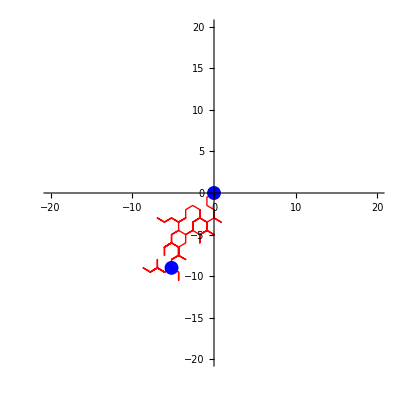

#### Uniformly biased walks

To produce biased walks of the type illustrated in a previous figure, set

```mathematica
wr[x_,y_]:={6,3,1}
wb[x_,y_]:={6,3,1}
```

of which this is a selected (but—so diverse are they—hardly "typical) example:

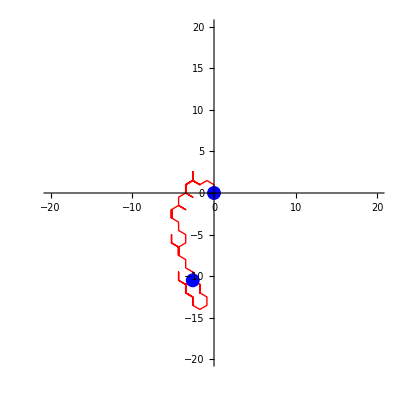

#### Red-blue differentiated uniformly biased

Write (say)

```mathematica
wr[x_,y_]:={6,3,1}
wb[x_,y_]:={1,4,4}
```

to indicate that all red nodes present the same site-independent set of unbalanced weights, ditto all blue nodes, but the red/blue nodes are distinctly unbalanced.

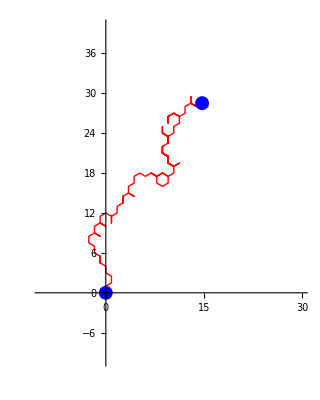

REMARK: Most of those figures show a similar trend. I should be possible to extract a "predicted mean slope" from the invariant weights {6, 3, 1} and {1, 4, 4}.

#### Simple model of "corrugation"

Assuming that the corrugations run parallel to the y-axis we expect the weight functions to be y-independent, functions only of x. And from the figure

-Graphics-

we expect ℛ2 and ℬ3 to be identically, ditto ℛ3 and ℬ2. Looking to

```mathematica
wr[x_,y_]:={0,2/3+1/2 Cos[(2π)/5 x],2/3-1/2 Cos[(2π)/5 x]}
wb[x_,y_]:={0,2/3-1/2 Cos[(2π)/5 x],2/3+1/2 Cos[(2π)/5 x]}
```

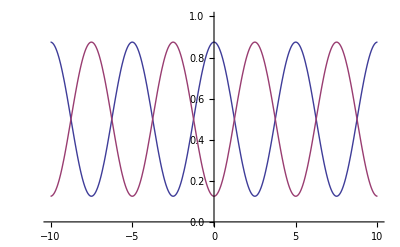

```mathematica
Plot[{(2/3+1/2 Cos[(2π)/5 x])/(4/3),(2/3-1/2 Cos[(2π)/5 x])/(4/3)},{x,-10,10},PlotRange->{0,1}]
```

we get densely over-written walks of the form

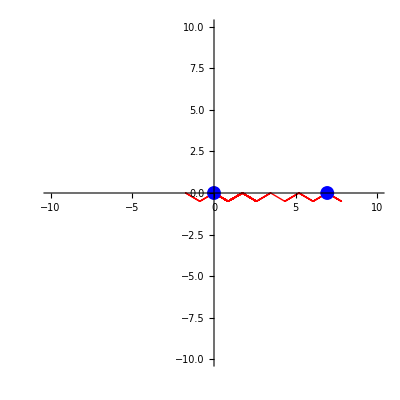

To reduce the overwrite we introduce some probability of drift up the y-axis:

```mathematica
wr[x_,y_]:={1/10,2/3+1/2 Cos[(2π)/5 x],2/3-1/2 Cos[(2π)/5 x]}
wb[x_,y_]:={0,2/3-1/2 Cos[(2π)/5 x],2/3+1/2 Cos[(2π)/5 x]}
```

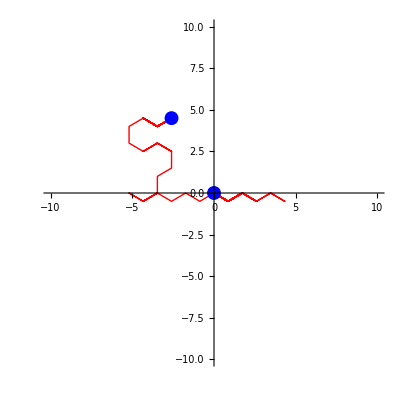

```mathematica
Subscript[P, 0]={0,0};
Subscript[P, 1]=RandomChoice[wr[Subscript[P, 0]⟦1⟧,Subscript[P, 0]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 0];
Subscript[P, 2]=RandomChoice[wb[Subscript[P, 1]⟦1⟧,Subscript[P, 1]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 1];
Subscript[P, 3]=RandomChoice[wr[Subscript[P, 2]⟦1⟧,Subscript[P, 2]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 2];
Subscript[P, 4]=RandomChoice[wb[Subscript[P, 3]⟦1⟧,Subscript[P, 3]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 3];
Subscript[P, 5]=RandomChoice[wr[Subscript[P, 4]⟦1⟧,Subscript[P, 4]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 4];
Subscript[P, 6]=RandomChoice[wb[Subscript[P, 5]⟦1⟧,Subscript[P, 5]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 5];
Subscript[P, 7]=RandomChoice[wr[Subscript[P, 6]⟦1⟧,Subscript[P, 6]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 6];
Subscript[P, 8]=RandomChoice[wb[Subscript[P, 7]⟦1⟧,Subscript[P, 7]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 7];
Subscript[P, 9]=RandomChoice[wr[Subscript[P, 8]⟦1⟧,Subscript[P, 8]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 8];
Subscript[P, 10]=RandomChoice[wb[Subscript[P, 9]⟦1⟧,Subscript[P, 9]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 9];
Subscript[P, 11]=RandomChoice[wr[Subscript[P, 10]⟦1⟧,Subscript[P, 10]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 10];
Subscript[P, 12]=RandomChoice[wb[Subscript[P, 11]⟦1⟧,Subscript[P, 11]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 11];
Subscript[P, 13]=RandomChoice[wr[Subscript[P, 12]⟦1⟧,Subscript[P, 12]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 12];
Subscript[P, 14]=RandomChoice[wb[Subscript[P, 13]⟦1⟧,Subscript[P, 13]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 13];
Subscript[P, 15]=RandomChoice[wr[Subscript[P, 14]⟦1⟧,Subscript[P, 14]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 14];
Subscript[P, 16]=RandomChoice[wb[Subscript[P, 15]⟦1⟧,Subscript[P, 15]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 15];
Subscript[P, 17]=RandomChoice[wr[Subscript[P, 16]⟦1⟧,Subscript[P, 16]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 16];
Subscript[P, 18]=RandomChoice[wb[Subscript[P, 17]⟦1⟧,Subscript[P, 17]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 17];
Subscript[P, 19]=RandomChoice[wr[Subscript[P, 18]⟦1⟧,Subscript[P, 18]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 18];
Subscript[P, 20]=RandomChoice[wb[Subscript[P, 19]⟦1⟧,Subscript[P, 19]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 19];
Subscript[P, 21]=RandomChoice[wr[Subscript[P, 20]⟦1⟧,Subscript[P, 20]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 20];
Subscript[P, 22]=RandomChoice[wb[Subscript[P, 21]⟦1⟧,Subscript[P, 21]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 21];
Subscript[P, 23]=RandomChoice[wr[Subscript[P, 22]⟦1⟧,Subscript[P, 22]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 22];
Subscript[P, 24]=RandomChoice[wb[Subscript[P, 23]⟦1⟧,Subscript[P, 23]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 23];
Subscript[P, 25]=RandomChoice[wr[Subscript[P, 24]⟦1⟧,Subscript[P, 24]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 24];
Subscript[P, 26]=RandomChoice[wb[Subscript[P, 25]⟦1⟧,Subscript[P, 25]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 25];
Subscript[P, 27]=RandomChoice[wr[Subscript[P, 26]⟦1⟧,Subscript[P, 26]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 26];
Subscript[P, 28]=RandomChoice[wb[Subscript[P, 27]⟦1⟧,Subscript[P, 27]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 27];
Subscript[P, 29]=RandomChoice[wr[Subscript[P, 28]⟦1⟧,Subscript[P, 28]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 28];
Subscript[P, 30]=RandomChoice[wb[Subscript[P, 29]⟦1⟧,Subscript[P, 29]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 29];
Subscript[P, 31]=RandomChoice[wr[Subscript[P, 30]⟦1⟧,Subscript[P, 30]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 30];
Subscript[P, 32]=RandomChoice[wb[Subscript[P, 31]⟦1⟧,Subscript[P, 31]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 31];
Subscript[P, 33]=RandomChoice[wr[Subscript[P, 32]⟦1⟧,Subscript[P, 32]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 32];
Subscript[P, 34]=RandomChoice[wb[Subscript[P, 33]⟦1⟧,Subscript[P, 33]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 33];
Subscript[P, 35]=RandomChoice[wr[Subscript[P, 34]⟦1⟧,Subscript[P, 34]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 34];
Subscript[P, 36]=RandomChoice[wb[Subscript[P, 35]⟦1⟧,Subscript[P, 35]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 35];
Subscript[P, 37]=RandomChoice[wr[Subscript[P, 36]⟦1⟧,Subscript[P, 36]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 36];
Subscript[P, 38]=RandomChoice[wb[Subscript[P, 37]⟦1⟧,Subscript[P, 37]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 37];
Subscript[P, 39]=RandomChoice[wr[Subscript[P, 38]⟦1⟧,Subscript[P, 38]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 38];
Subscript[P, 40]=RandomChoice[wb[Subscript[P, 39]⟦1⟧,Subscript[P, 39]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 39];
Subscript[P, 41]=RandomChoice[wr[Subscript[P, 40]⟦1⟧,Subscript[P, 40]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 40];
Subscript[P, 42]=RandomChoice[wb[Subscript[P, 41]⟦1⟧,Subscript[P, 41]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 41];
Subscript[P, 43]=RandomChoice[wr[Subscript[P, 42]⟦1⟧,Subscript[P, 42]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 42];
Subscript[P, 44]=RandomChoice[wb[Subscript[P, 43]⟦1⟧,Subscript[P, 43]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 43];
Subscript[P, 45]=RandomChoice[wr[Subscript[P, 44]⟦1⟧,Subscript[P, 44]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 44];
Subscript[P, 46]=RandomChoice[wb[Subscript[P, 45]⟦1⟧,Subscript[P, 45]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 45];
Subscript[P, 47]=RandomChoice[wr[Subscript[P, 46]⟦1⟧,Subscript[P, 46]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 46];
Subscript[P, 48]=RandomChoice[wb[Subscript[P, 47]⟦1⟧,Subscript[P, 47]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 47];
Subscript[P, 49]=RandomChoice[wr[Subscript[P, 48]⟦1⟧,Subscript[P, 48]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 48];
Subscript[P, 50]=RandomChoice[wb[Subscript[P, 49]⟦1⟧,Subscript[P, 49]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 49];
Subscript[P, 51]=RandomChoice[wr[Subscript[P, 50]⟦1⟧,Subscript[P, 50]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 50];
Subscript[P, 52]=RandomChoice[wb[Subscript[P, 51]⟦1⟧,Subscript[P, 51]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 51];
Subscript[P, 53]=RandomChoice[wr[Subscript[P, 52]⟦1⟧,Subscript[P, 52]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 52];
Subscript[P, 54]=RandomChoice[wb[Subscript[P, 53]⟦1⟧,Subscript[P, 53]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 53];
Subscript[P, 55]=RandomChoice[wr[Subscript[P, 54]⟦1⟧,Subscript[P, 54]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 54];
Subscript[P, 56]=RandomChoice[wb[Subscript[P, 55]⟦1⟧,Subscript[P, 55]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 55];
Subscript[P, 57]=RandomChoice[wr[Subscript[P, 56]⟦1⟧,Subscript[P, 56]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 56];
Subscript[P, 58]=RandomChoice[wb[Subscript[P, 57]⟦1⟧,Subscript[P, 57]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 57];
Subscript[P, 59]=RandomChoice[wr[Subscript[P, 58]⟦1⟧,Subscript[P, 58]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 58];
Subscript[P, 60]=RandomChoice[wb[Subscript[P, 59]⟦1⟧,Subscript[P, 59]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 59];
Subscript[P, 61]=RandomChoice[wr[Subscript[P, 60]⟦1⟧,Subscript[P, 60]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 60];
Subscript[P, 62]=RandomChoice[wb[Subscript[P, 61]⟦1⟧,Subscript[P, 61]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 61];
Subscript[P, 63]=RandomChoice[wr[Subscript[P, 62]⟦1⟧,Subscript[P, 62]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 62];
Subscript[P, 64]=RandomChoice[wb[Subscript[P, 63]⟦1⟧,Subscript[P, 63]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 63];
Subscript[P, 65]=RandomChoice[wr[Subscript[P, 64]⟦1⟧,Subscript[P, 64]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 64];
Subscript[P, 66]=RandomChoice[wb[Subscript[P, 65]⟦1⟧,Subscript[P, 65]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 65];
Subscript[P, 67]=RandomChoice[wr[Subscript[P, 66]⟦1⟧,Subscript[P, 66]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 66];
Subscript[P, 68]=RandomChoice[wb[Subscript[P, 67]⟦1⟧,Subscript[P, 67]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 67];
Subscript[P, 69]=RandomChoice[wr[Subscript[P, 68]⟦1⟧,Subscript[P, 68]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 68];
Subscript[P, 70]=RandomChoice[wb[Subscript[P, 69]⟦1⟧,Subscript[P, 69]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 69];
Subscript[P, 71]=RandomChoice[wr[Subscript[P, 70]⟦1⟧,Subscript[P, 70]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 70];
Subscript[P, 72]=RandomChoice[wb[Subscript[P, 71]⟦1⟧,Subscript[P, 71]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 71];
Subscript[P, 73]=RandomChoice[wr[Subscript[P, 72]⟦1⟧,Subscript[P, 72]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 72];
Subscript[P, 74]=RandomChoice[wb[Subscript[P, 73]⟦1⟧,Subscript[P, 73]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 73];
Subscript[P, 75]=RandomChoice[wr[Subscript[P, 74]⟦1⟧,Subscript[P, 74]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 74];
Subscript[P, 76]=RandomChoice[wb[Subscript[P, 75]⟦1⟧,Subscript[P, 75]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 75];
Subscript[P, 77]=RandomChoice[wr[Subscript[P, 76]⟦1⟧,Subscript[P, 76]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 76];
Subscript[P, 78]=RandomChoice[wb[Subscript[P, 77]⟦1⟧,Subscript[P, 77]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 77];
Subscript[P, 79]=RandomChoice[wr[Subscript[P, 78]⟦1⟧,Subscript[P, 78]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 78];
Subscript[P, 80]=RandomChoice[wb[Subscript[P, 79]⟦1⟧,Subscript[P, 79]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 79];
Subscript[P, 81]=RandomChoice[wr[Subscript[P, 80]⟦1⟧,Subscript[P, 80]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 80];
Subscript[P, 82]=RandomChoice[wb[Subscript[P, 81]⟦1⟧,Subscript[P, 81]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 81];
Subscript[P, 83]=RandomChoice[wr[Subscript[P, 82]⟦1⟧,Subscript[P, 82]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 82];
Subscript[P, 84]=RandomChoice[wb[Subscript[P, 83]⟦1⟧,Subscript[P, 83]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 83];
Subscript[P, 85]=RandomChoice[wr[Subscript[P, 84]⟦1⟧,Subscript[P, 84]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 84];
Subscript[P, 86]=RandomChoice[wb[Subscript[P, 85]⟦1⟧,Subscript[P, 85]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 85];
Subscript[P, 87]=RandomChoice[wr[Subscript[P, 86]⟦1⟧,Subscript[P, 86]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 86];
Subscript[P, 88]=RandomChoice[wb[Subscript[P, 87]⟦1⟧,Subscript[P, 87]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 87];
Subscript[P, 89]=RandomChoice[wr[Subscript[P, 88]⟦1⟧,Subscript[P, 88]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 88];
Subscript[P, 90]=RandomChoice[wb[Subscript[P, 89]⟦1⟧,Subscript[P, 89]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 89];
Subscript[P, 91]=RandomChoice[wr[Subscript[P, 90]⟦1⟧,Subscript[P, 90]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 90];
Subscript[P, 92]=RandomChoice[wb[Subscript[P, 91]⟦1⟧,Subscript[P, 91]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 91];
Subscript[P, 93]=RandomChoice[wr[Subscript[P, 92]⟦1⟧,Subscript[P, 92]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 92];
Subscript[P, 94]=RandomChoice[wb[Subscript[P, 93]⟦1⟧,Subscript[P, 93]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 93];
Subscript[P, 95]=RandomChoice[wr[Subscript[P, 94]⟦1⟧,Subscript[P, 94]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 94];
Subscript[P, 96]=RandomChoice[wb[Subscript[P, 95]⟦1⟧,Subscript[P, 95]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 95];
Subscript[P, 97]=RandomChoice[wr[Subscript[P, 96]⟦1⟧,Subscript[P, 96]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 96];
Subscript[P, 98]=RandomChoice[wb[Subscript[P, 97]⟦1⟧,Subscript[P, 97]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 97];
Subscript[P, 99]=RandomChoice[wr[Subscript[P, 98]⟦1⟧,Subscript[P, 98]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 98];
Subscript[P, 100]=RandomChoice[wb[Subscript[P, 99]⟦1⟧,Subscript[P, 99]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 99];


HexPath=ListLinePlot[Table[Subscript[P, k],{k,0,100}],AspectRatio->Automatic, PlotRange->{{-10,10},{-10,10}}, PlotStyle->{Thick, Red}];
Endpoints=Graphics[{{Blue, PointSize[0.025],Point[Subscript[P, 0]]},
{Blue, PointSize[0.025],Point[Subscript[P, 100]]}}];
Show[{HexPath, Endpoints}]
```

We find that such walks tend to be bounded on left and right by ∓5.

### Concluding Remarks

One could extend my 100-command sequence to (say) 200 without much difficulty, and even to 1000 with an hour or so of tedious work. But one would need to find a way to automate that procedure if one were interested in really long walks. Relatedly, there is a limit to what one can learn from one or a few illustrative walks; one needs to devise a way to automate the construction of many walks if one wants to use a Monte Carlo technique to extract persistent general features of such walks.

Physically, I can imagine writing something like

```mathematica
ℍ=∑_(all hex neighbor sets) Subscript[𝕒, i] Subscript[𝕒, j]
```

to set up the quantum theory of electron (exiton?) motion on graphene, but do not see how one gets from there to a picture of electrons "hopping" from sites to nearest-neighbor sites. The methods used to study Markov processes (matrix-driven evolution of a stochastic vector) would seem more apt…the problem there being that such matrices/vectors would necessarily be very high dimensional. And it is not easy so see how matrix elements in rectangular  array are most naturally to be associated with lattice nodes in hexagonal array.

Finally, one needs a physically-motivated rationale for assigning structure to the weight functions wr[x, y] and wb[x, y].

In short, I remain doubtful that study of random walks on currugated graphene provides a good way to study the quantum physics of such a system.